# Running in the Rain

## Predicting Runs based on Environmental Data

Stephen Schroeder

## Introduction

I have been running for several years now, and in September of 2017 I decided that I would start a "run streak." A running streak is defined as running at least 1 mile (1.61 km) every calendar day consecutively. I did this mostly because I found that I couldn't stick to only running 3 or 4 days a week - I would suddenly find myself not having run for several weeks or months! 

Now, almost two years later I have ideas about things that might affect my running, but Wolfram Language allows for so much interesting analysis to be done with my data tracked using RunKeeper! Normally I don’t go out with a plan for how long I will run, and I turn back based on how I am feeling that day. Because of this, one of the main questions that I have about my running data is how my running is affected by temperature. I know that I run less in the Canadian winter, but exactly how much less?

## Running Data Preparation

### Importing Running Data

Previously, I used ServiceConnect to fetch my running data, but unfortunately ServiceConnect does not fetch GPS data from RunKeeper which I will need to be able to get environmental data based on the location, date, and time of my run. 
So, I manually exported my data from my RunKeeper account as explained here, and saved the data to my NotebookDirectory[] with all the GPS files in their own folder. Now, to get started, all the data needs to be imported. I imported the data in a similar fashion to this fantastic Wolfram Blog post, where the running data is parsed using the smart SemanticImport using the column types of the .csv file from RunKeeper.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = SemanticImport[
	"cardioActivities.csv",
	{"String","Date","String","String",Restricted["Quantity","Kilometers"],
	"String","String",Restricted["Quantity",("Kilometers")/("Hours")],Restricted["Quantity","LargeCalories"],
	Restricted["Quantity","Meters"],"String","String","String","String"
	}
];
```

The GPS Data is slightly more difficult to work with, as each of the 651 runs that I exported have their own .GPX file, and to best deal with the data I only want the coordinates that were recorded at the very beginning of the run.

```mathematica
importGPSData[] := importGPSData[FileNames["*.gpx", "GPS"]]
importGPSData[files_List] := Association@ Map[importGPSData, files]
importGPSData[file_String] :=FileNameTake[file] ->  First @ Cases[
Import[file, "XML"], XMLElement["trkpt",{"lat"->lat_,"lon"->lon_},{_,XMLElement["time",{},{time_}]}] :> {time, lat, lon}, 
Infinity
];

rawGPSData = importGPSData[];
```

Now, so I can best use the GPS data, I will make sure that it is explicitly made up of lists of GeoPositions

```mathematica
GPSData = Map[
GeoPosition@{ToExpression[#[[2]]], ToExpression[#[[3]]]} &, 
rawGPSData
];
```

Lastly, the data needs to be added alongside the rest of the running data imported earlier into our now nice looking dataset!

```mathematica
runningDataWithGPS = Map[
Append[#, "GeoCoord" -> GPSData[#["GPX File"]]]&,
runningData
]
```

For my own sake, I will export the data so I don’t need to do it every time.

```mathematica
Export["RunStartCoords.dat",runningDataWithGPS]
```

RunStartCoords.dat

```mathematica
runningDataWithGPS=Import["RunStartCoords.dat"]
```

## Data Visualisation and Evaluation

Now it' s possible to do some basic visualisation of my running data. First, we can see the starting locations of my runs over the past ~2 years

```mathematica
GeoGraphics[GeoMarker[Cases[Import["RunStartCoords.dat"],{_,_}]]]
```

-Graphics-

The next plot provides real evidence that I do run more during the summer months! There seems like there must be a correlation based on temperature at the very least.

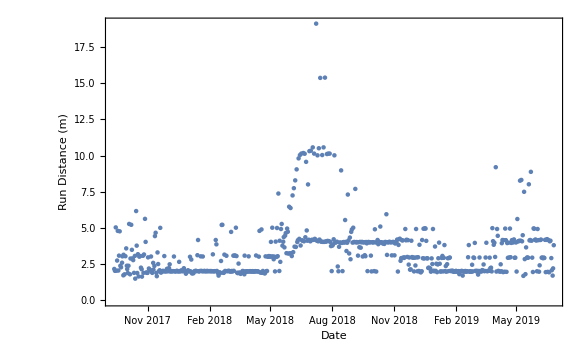

```mathematica
DateListPlot[Query[All,{"Date","Distance (km)"}]@data,Axes->True,FrameLabel->{"Date","Run Distance (m)"},Joined->False,PlotRange->All]
```

The next step is to determine pair the temperature at the time and location of my run with the distance of my run:

```mathematica
Query[All,"Date"]@data//Normal
```

{Tue 25 Jun 2019 07:34:44GMT-4.,Mon 24 Jun 2019 07:33:12GMT-4.,Sun 23 Jun 2019 15:32:53GMT-4.,Sat 22 Jun 2019 09:30:51GMT-4.,Fri 21 Jun 2019 15:55:01GMT-4.,Thu 20 Jun 2019 10:10:17GMT-4.,Wed 19 Jun 2019 09:59:59GMT-4.,Tue 18 Jun 2019 08:37:15GMT-4.,Mon 17 Jun 2019 10:11:56GMT-4.,Sun 16 Jun 2019 08:54:25GMT-4.,632,Wed 20 Sep 2017 07:35:32GMT-4.,Tue 19 Sep 2017 08:10:44GMT-4.,Mon 18 Sep 2017 07:44:49GMT-4.,Sun 17 Sep 2017 11:49:56GMT-4.,Sat 16 Sep 2017 12:47:00GMT-4.,Fri 15 Sep 2017 07:41:05GMT-4.,Thu 14 Sep 2017 11:41:37GMT-4.,Wed 13 Sep 2017 08:03:57GMT-4.,Tue 12 Sep 2017 07:00:48GMT-4.}
 |  |  |  |

```mathematica
Import["RunStartCoords.dat"]
```

{{42.3863,-71.2224},{42.3865,-71.2223},{42.3863,-71.2224},{51.0718,-114.091},{51.0718,-114.092},{51.0717,-114.091},{51.0718,-114.092},{51.0719,-114.092},{51.0718,-114.091},{51.0717,-114.091},{51.0717,-114.092},{51.0717,-114.091},{51.0717,-114.091},{51.0717,-114.091},{51.0717,-114.091},{51.0718,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0717,-114.092},{51.0717,-114.092},{51.0717,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0718,-114.091},{51.0717,-114.091},{51.0718,-114.092},{51.072,-114.092},{51.0717,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0717,-114.092},{51.0717,-114.092},{51.0719,-114.092},{51.0717,-114.091},{51.0719,-114.092},{51.0718,-114.092},{51.0716,-114.092},{51.0716,-114.091},{51.0718,-114.092},{46.8091,-71.2198},{$Failed},{46.8091,-71.22},{46.8093,-71.217},{46.8091,-71.2196},{$Failed},{41.4831,-81.7027},{41.4833,-81.7026},{41.4831,-81.7024},{41.483,-81.7026},{41.4832,-81.7026},{41.4833,-81.7024},{41.4832,-81.703},{41.4832,-81.7027},{51.0718,-114.091},{51.0717,-114.091},{51.0719,-114.091},{51.0718,-114.091},{51.0717,-114.091},{51.0718,-114.091},{51.0718,-114.091},{51.0717,-114.092},{51.0718,-114.091},{51.0717,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0718,-114.091},{51.0718,-114.092},{51.0718,-114.091},{51.0717,-114.091},{51.072,-114.091},{51.0718,-114.092},{51.0718,-114.092},{51.0717,-114.092},{51.0718,-114.092},{51.0719,-114.091},{51.0718,-114.091},{51.0718,-114.092},{51.63,-121.3},{51.6301,-121.3},{51.0717,-114.091},{51.0718,-114.092},{51.0717,-114.092},{51.0718,-114.091},{51.0718,-114.091},{51.0718,-114.092},{51.0717,-114.091},{51.0718,-114.092},{51.0717,-114.092},{51.0718,-114.091},{51.0717,-114.092},{51.0717,-114.091},{53.5073,-113.286},{53.5074,-113.286},{51.0718,-114.091},{51.0716,-114.091},{51.0717,-114.092},{51.0717,-114.091},{51.0717,-114.091},{51.0717,-114.092},{51.0718,-114.091},{51.0717,-114.091},{51.0718,-114.092},{51.0718,-114.091},{51.0717,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0718,-114.091},{51.0717,-114.091},{51.0717,-114.091},{51.0718,-114.091},{51.0717,-114.091},{51.0717,-114.092},{51.0717,-114.091},{51.0717,-114.092},{51.0717,-114.091},{51.0718,-114.091},{51.0718,-114.091},{51.0717,-114.091},{51.0718,-114.091},{51.0717,-114.091},{51.0718,-114.091},{51.0717,-114.091},{51.0718,-114.091},{51.0717,-114.091},{51.0718,-114.092},{51.0718,-114.091},{51.0718,-114.092},{51.0717,-114.091},{51.0717,-114.091},{51.0717,-114.092},{51.0718,-114.091},{51.0717,-114.091},{51.0717,-114.091},{51.0718,-114.091},{51.0717,-114.091},{51.0717,-114.091},{51.0718,-114.091},{51.0718,-114.092},{51.0717,-114.091},{51.0718,-114.092},{51.0717,-114.092},{51.0717,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.091},{51.072,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.091},{51.0719,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0717,-114.092},{51.0719,-114.091},{51.0718,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0718,-114.091},{51.0718,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0719,-114.091},{51.0719,-114.092},{51.0719,-114.091},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0717,-114.092},{53.5073,-113.286},{53.5074,-113.286},{53.5074,-113.286},{53.5075,-113.286},{51.0718,-114.091},{51.0718,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0719,-114.092},{44.9882,-122.988},{51.0719,-114.092},{51.0717,-114.092},{51.0719,-114.092},{51.0718,-114.091},{51.0719,-114.092},{51.0717,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0719,-114.091},{51.0718,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0718,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.091},{51.0719,-114.092},{51.0719,-114.092},{51.0719,-114.092},{51.0718,-114.092},{51.0718,-114.091},{51.0718,-114.092},{51.0719,-114.092},{51.0718,-114.091},{51.0718,-114.092},{51.0718,-114.091},{51.0717,-114.092},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0886,-114.166},{51.0918,-114.158},{51.0918,-114.158},{51.0606,-114.115},{51.0606,-114.115},{51.0606,-114.115},{51.0918,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0917,-114.158},{53.5074,-113.286},{53.5073,-113.286},{51.0917,-114.158},{51.0918,-114.158},{51.0916,-114.159},{51.0918,-114.158},{51.0917,-114.159},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.159},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.159},{51.0918,-114.158},{51.0918,-114.159},{51.0917,-114.159},{51.0918,-114.158},{51.0917,-114.159},{51.0917,-114.159},{51.0918,-114.158},{51.0918,-114.158},{51.0606,-114.115},{51.0606,-114.115},{51.0606,-114.115},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.159},{51.0916,-114.159},{51.0918,-114.158},{49.2997,-117.658},{49.2999,-117.657},{49.2999,-117.658},{49.2995,-117.658},{49.2999,-117.658},{51.0977,-115.358},{51.0977,-115.358},{51.0977,-115.358},{51.0976,-115.358},{51.0976,-115.358},{51.0918,-114.158},{51.4516,-112.701},{51.4516,-112.701},{51.4518,-112.701},{51.0917,-114.159},{51.0918,-114.158},{51.0917,-114.159},{51.0917,-114.159},{51.0917,-114.159},{51.0918,-114.158},{51.0917,-114.159},{51.0918,-114.158},{49.4012,8.66925},{49.4016,8.66901},{49.4016,8.66935},{49.4015,8.66941},{49.4014,8.66924},{49.4014,8.66916},{49.4016,8.66944},{49.4014,8.66926},{49.4019,8.66944},{49.4016,8.66933},{49.4015,8.66917},{49.4013,8.66925},{49.4012,8.66891},{49.4017,8.66939},{49.4015,8.66912},{49.4015,8.6692},{49.4013,8.66915},{49.4017,8.66931},{49.4013,8.66925},{49.4013,8.66917},{49.4013,8.66912},{49.4014,8.66913},{49.4013,8.66922},{49.4015,8.66945},{49.4015,8.66924},{49.4017,8.6694},{49.4014,8.66928},{49.4016,8.66943},{49.4013,8.66914},{49.4014,8.66907},{49.4015,8.66917},{49.4015,8.66918},{49.4015,8.66943},{49.4017,8.6693},{49.4019,8.66943},{49.4015,8.6692},{49.4016,8.66926},{49.4015,8.66918},{49.4016,8.6694},{49.4016,8.6693},{49.4015,8.66918},{49.4016,8.66928},{49.4019,8.66914},{49.4016,8.66937},{49.4017,8.66934},{49.4015,8.6692},{49.403,8.66872},{49.4016,8.66934},{49.4014,8.66934},{49.4013,8.66912},{49.4016,8.66927},{49.4015,8.66918},{49.4015,8.66933},{49.4015,8.66927},{49.4016,8.66922},{49.4016,8.66959},{49.4014,8.66937},{49.4015,8.66924},{49.4016,8.66927},{49.402,8.66878},{49.4017,8.6695},{49.4018,8.66906},{49.4015,8.66922},{49.4015,8.6692},{49.4015,8.66948},{49.4015,8.66943},{49.4017,8.66952},{49.4015,8.66953},{49.4016,8.66956},{49.402,8.66871},{49.4015,8.66911},{49.4016,8.66931},{49.4016,8.66904},{49.4014,8.66926},{49.4011,8.66934},{49.4015,8.66906},{49.4015,8.66923},{49.4016,8.66945},{49.4016,8.66954},{49.4016,8.6696},{49.4018,8.66923},{49.4016,8.66917},{49.4014,8.66933},{49.4017,8.66937},{49.4016,8.66957},{49.4015,8.66945},{49.4017,8.66945},{49.4018,8.66924},{49.4018,8.66942},{49.4016,8.66924},{51.0918,-114.159},{51.0918,-114.159},{51.0917,-114.159},{$Failed},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.3498,-110.481},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.159},{51.0918,-114.158},{51.0917,-114.158},{51.0606,-114.115},{51.0606,-114.115},{51.0607,-114.115},{51.0606,-114.115},{51.0606,-114.115},{51.0606,-114.115},{51.0607,-114.115},{51.0606,-114.115},{51.0605,-114.115},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.159},{51.3498,-110.48},{51.0918,-114.158},{51.0918,-114.159},{51.0918,-114.159},{51.0918,-114.158},{51.0917,-114.158},{51.0606,-114.115},{51.0606,-114.115},{51.0603,-114.115},{51.0606,-114.115},{51.0606,-114.115},{51.0641,-114.152},{51.0604,-114.115},{51.0606,-114.115},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.159},{51.0917,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.159},{51.0917,-114.159},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.159},{51.0917,-114.158},{51.0917,-114.158},{51.0606,-114.115},{51.0607,-114.115},{51.0606,-114.115},{51.0605,-114.115},{51.0606,-114.115},{51.0607,-114.115},{51.0606,-114.115},{51.0606,-114.115},{51.0605,-114.115},{51.0606,-114.115},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.0917,-114.158},{51.0917,-114.159},{51.0918,-114.158},{51.0917,-114.159},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.16},{51.0918,-114.158},{51.0917,-114.159},{51.0917,-114.158},{51.0916,-114.159},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.159},{51.0917,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.159},{51.0918,-114.159},{51.0918,-114.159},{51.0917,-114.158},{51.0606,-114.115},{51.0607,-114.115},{51.0606,-114.115},{51.0605,-114.115},{51.0917,-114.159},{51.0917,-114.159},{51.0918,-114.159},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0602,-114.115},{51.0606,-114.115},{51.1015,-114.162},{53.5074,-113.286},{53.5065,-113.286},{51.0918,-114.158},{51.0916,-114.159},{51.0917,-114.159},{51.0917,-114.159},{51.0918,-114.158},{51.0917,-114.158},{51.0918,-114.158},{51.0919,-114.158},{51.0918,-114.158},{51.0917,-114.159},{51.0917,-114.158},{51.0918,-114.158},{51.0916,-114.159},{51.0918,-114.159},{51.0918,-114.158},{51.0918,-114.158},{51.0918,-114.158},{51.0917,-114.158},{51.092,-114.158},{51.4172,-116.21},{51.4169,-116.21},{51.0917,-114.159},{51.0917,-114.159},{51.0932,-114.155},{51.0917,-114.158},{51.0917,-114.159},{51.0917,-114.159},{51.0917,-114.159},{51.0918,-114.159},{51.0916,-114.159},{51.0917,-114.158},{51.0606,-114.115},{51.0606,-114.115},{51.0606,-114.115},{51.0606,-114.115},{51.0918,-114.158},{51.0913,-114.162},{51.0917,-114.161},{51.091,-114.162},{$Failed},{51.0913,-114.162},{51.0862,-114.165},{51.0917,-114.16},{51.0916,-114.159},{51.0992,-114.161},{$Failed},{51.0927,-114.158},{51.0916,-114.161},{$Failed},{$Failed},{$Failed},{51.0897,-114.165},{$Failed},{$Failed},{51.0903,-114.162},{51.0916,-114.162},{51.0861,-114.165},{51.0868,-114.165},{$Failed},{51.0917,-114.161},{51.0914,-114.161},{51.0918,-114.16},{51.0606,-114.115},{51.0917,-114.16},{51.0917,-114.161},{51.0917,-114.16},{51.0917,-114.159},{51.0916,-114.155},{51.0914,-114.162},{51.0911,-114.162},{51.091,-114.162},{51.0918,-114.16},{$Failed},{51.0902,-114.163},{51.09,-114.165},{51.0856,-114.164},{51.0936,-114.159},{51.0915,-114.162},{$Failed},{51.0901,-114.163},{51.0903,-114.163},{51.0918,-114.16},{51.0629,-114.117},{51.0609,-114.115},{51.06,-114.114},{51.0884,-114.165},{$Failed},{$Failed},{51.0916,-114.162},{$Failed},{51.0975,-114.161},{51.0873,-114.165},{51.0869,-114.165},{51.0935,-114.162},{51.0908,-114.162},{51.0936,-114.162},{51.0938,-114.159},{$Failed},{51.0934,-114.159},{51.092,-114.159},{51.0936,-114.16},{51.0935,-114.16}}

```mathematica
WeatherData[,"Temperature",]
```

Function::slotn: Slot number 2 in WeatherData[#1,Temperature,#2]& cannot be filled from (WeatherData[#1,Temperature,#2]&)[{42.3863,-71.2224}].

WeatherData::notent: {42.386333, -71.222367} is not a known entity, class, or tag for WeatherData. Use WeatherData[] for a list of entities.

Function::slotn: Slot number 2 in WeatherData[#1,Temperature,#2]& cannot be filled from (WeatherData[#1,Temperature,#2]&)[DateObject[{2019,6,25,7,34,44},Instant,Gregorian,-4.]].

WeatherData::notent: DateObject[{2019, 6, 25, 7, 34, 44}, "Instant", "Gregorian", -4.] is not a known entity, class, or tag for WeatherData. Use WeatherData[] for a list of entities.

Function::slotn: Slot number 2 in WeatherData[#1,Temperature,#2]& cannot be filled from (WeatherData[#1,Temperature,#2]&)[{42.3865,-71.2223}].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

WeatherData::notent: {42.386455, -71.222277} is not a known entity, class, or tag for WeatherData. Use WeatherData[] for a list of entities.

General::stop: Further output of WeatherData::notent will be suppressed during this calculation.

{WeatherData[{42.3863,-71.2224},Temperature,#2],WeatherData[Tue 25 Jun 2019 07:34:44GMT-4.,Temperature,#2],WeatherData[{42.3865,-71.2223},Temperature,#2],WeatherData[Mon 24 Jun 2019 07:33:12GMT-4.,Temperature,#2],WeatherData[{42.3863,-71.2224},Temperature,#2],WeatherData[Sun 23 Jun 2019 15:32:53GMT-4.,Temperature,#2],1291,WeatherData[Thu 14 Sep 2017 11:41:37GMT-4.,Temperature,#2],WeatherData[{51.0936,-114.16},Temperature,#2],WeatherData[Wed 13 Sep 2017 08:03:57GMT-4.,Temperature,#2],WeatherData[{51.0935,-114.16},Temperature,#2],WeatherData[Tue 12 Sep 2017 07:00:48GMT-4.,Temperature,#2]}
 |  |  |  |

```mathematica
WeatherData["Properties"]
```

{AlternateStandardNames,CloudCoverFraction,CloudHeight,CloudTypes,Conditions,Coordinates,DewPoint,Elevation,Humidity,Latitude,Longitude,MaxTemperature,MaxWindSpeed,MeanDewPoint,MeanHumidity,MeanPressure,MeanStationPressure,MeanTemperature,MeanVisibility,MeanWindChill,MeanWindSpeed,Memberships,MinTemperature,NCDCID,PrecipitationAmount,PrecipitationRate,PrecipitationTypes,Pressure,PressureTendency,SnowAccumulation,SnowAccumulationRate,SnowDepth,StationName,StationPressure,Temperature,TotalPrecipitation,Visibility,WBANID,WindChill,WindDirection,WindGusts,WindSpeed,WMOID}

```mathematica
GeoGraphics[GeoMarker[GeoPosition[{42.386333, -71.222367}]]]
```

-Graphics-